Project Title

Chen, Matthew

Grankovsky, Vladimir

Carnegie Mellon University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT:
OCR (Optical Character Recognition) for all Unicode characters

SUMMARY OF WORK:
OCR supporting 8 major writing systems: Latin, Chinese, Arabic, Devanagari, Cyrillic, Japanese, Korean, and Greek

RESULTS AND FUTURE  WORK:
90% accuracy recognizing handwritten characters; train on more fonts, support more writing systems and ultimately all Unicode characters

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

I developed my neural network based on LeNet by adding batch normalization layers, dropout layers, and more convolutional layers. I trained my neural network on characters of different rotations and fonts imitating handwritten styles generated by Mathematica. I first tried LeNet on my computer with small samples of Chinese characters sizing from 16 to 1024, which worked averagely on handwritten characters. To classify more characters, I made my network deeper and improved my algorithm for generating images by replacing Rasterize by Image, Graphics, and Text. To train on all 21000 Chinese characters, I used services provided by AWS to accelerate the training process and the trained network performed well on handwritten characters. Finally I added 7 more writing systems and trained on over 32000 characters.

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail
OCR supporting 8 major writing systems: Latin, Chinese, Arabic, Devanagari, Cyrillic, Japanese, Korean, and Greek
90% accuracy recognizing handwritten characters

Code
Neural Network:

OUCR=NetChain[{
ConvolutionLayer[32,{5,5},”PaddingSize”→{2,2},”Stride”→2],
BatchNormalizationLayer[“Input”→{32,32,32}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[64,{3,3},”PaddingSize”→{1,1}],
BatchNormalizationLayer[“Input”→{64,16,16}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[128,{3,3},”PaddingSize”→{1,1}],
BatchNormalizationLayer[“Input”→{128,8,8}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[256,{3,3},”PaddingSize”→{1,1}],
BatchNormalizationLayer[“Input”→{256,4,4}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[0.5],
LinearLayer[],
SoftmaxLayer[]
},
“Output”→NetDecoder[{“Class”,Unicode}],
“Input”→NetEncoder[{“Image”,{64,64},”Grayscale”,”MeanImage”→0.85}]
]

Generating training set:

trainingSetUpright[list_,size_,scale_,font_,horizontal_,vertical_]:=Module[{n,c,r},n=Length@list;c=Floor[Sqrt[n]];
r=Ceiling[n/c];
Thread[(Join@@ImagePartition[Image[Graphics[MapIndexed[Text[Style[#1,FontFamily→font,FontSize→Scaled[scale/c]],Reverse@#2]&,Reverse[Partition[FromCharacterCode/@list,UpTo[c]]],{2}],PlotRange→{{horizontal,c+horizontal},{vertical,r+vertical}},ImageSize→{size*c,size*r}],ColorSpace→”Grayscale”],size])[[;;n]]→FromCharacterCode/@list]]

trainingSetRotated[list_,size_,scale_,font_,rotateAngle_,horizontal_,vertical_]:=Module[{n,c,r},n=Length@list;c=Floor[Sqrt[n]];
r=Ceiling[n/c];
Thread[(Join@@ImagePartition[Image[Graphics[MapIndexed[Rotate[Text[Style[#1,FontFamily→font,FontSize→Scaled[scale/c]],Reverse@#2],RandomVariate[NormalDistribution[0,rotateAngle]] Degree]&,Reverse[Partition[FromCharacterCode/@list,UpTo[c]]],{2}],PlotRange→{{horizontal,c+horizontal},{vertical,r+vertical}},ImageSize→{size*c,size*r}],ColorSpace→”Grayscale”],size])[[;;n]]→FromCharacterCode/@list]]

Written Content / Lesson Plans

Conclusions in Detail

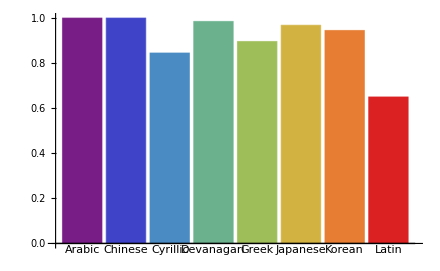
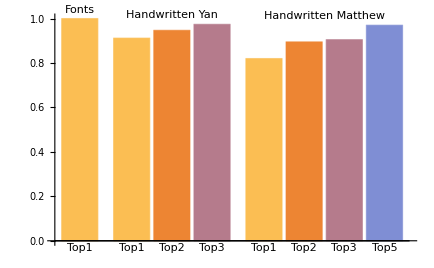
All Visualizations
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Data Sources Links/References

Future Directions
Train on more fonts, support more writing systems and ultimately all Unicode characters

Background Info Links/References

Keywords

OCR

Unicode

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```